```mathematica
datamedical ={{1,90},{2,107},{3,126},{4,145},{5,171},{6,188},{7,189},{8,190},{9,190},{10,190},{11,192},{12,192},{13,192},{14,192},{15,203},{16,203},{17,204}}
```

{{1,90},{2,107},{3,126},{4,145},{5,171},{6,188},{7,189},{8,190},{9,190},{10,190},{11,192},{12,192},{13,192},{14,192},{15,203},{16,203},{17,204}}

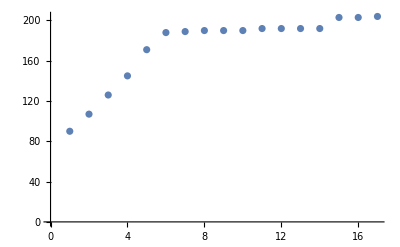

```mathematica
ListPlot[datamedical]
```

```mathematica
goel=NonlinearModelFit[datamedical,a*(1-Exp[-b*t]),{a,b},t]
```

FittedModel[197.386 (1-ⅇ^(-0.398518 t))]

```mathematica
Normal[goel]
```

197.386 (1-ⅇ^(-0.398518 t))

```mathematica
goel["BestFitParameters"]
```

{a→197.386,b→0.398518}

```mathematica
goel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 197.386 | 3.13651 | 62.9317 | 1.35741×10^-19
b | 0.398518 | 0.0296618 | 13.4354 | 9.09527×10^-10

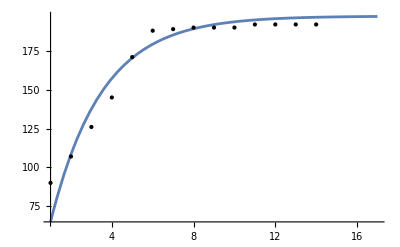

```mathematica
Plot[goel[t],{t,1,17},Epilog->Point[datamedical]]
```

```mathematica
delayedSshaped = NonlinearModelFit[datamedical,a(1-(1+b*t)Exp[-b*t]),{{a,200},b},t]
```

FittedModel[192.528 (1-ⅇ^(-0.881498 t) (1+0.881498 t))]

```mathematica
Normal[delayedSshaped]
```

174.353 (1-ⅇ^(-54.3125 t) (1+54.3125 t))

```mathematica
delayedSshaped["BestFitParameters"]
```

{a→174.353,b→54.3125}

```mathematica
delayedSshaped["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 192.528 | 4.49268 | 42.8538 | 4.19347×10^-17
b | 0.881498 | 0.0844456 | 10.4386 | 2.83234×10^-8

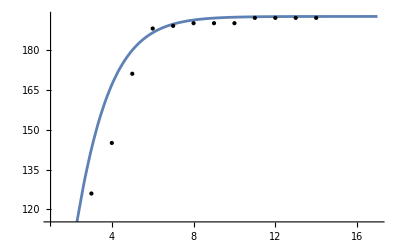

```mathematica
Plot[delayedSshaped[t],{t,1,17},Epilog->Point[datamedical]]
```

```mathematica
inflection = NonlinearModelFit[datamedical,(a*(1-Exp[-b*t]))/(1+beta*Exp[-b*t]),{{a,200},b,beta},t]
```

FittedModel[(203.473 (1-ⅇ^(-«20»«1»«1»)))/(1-0.608916 ⅇ^(-«20»«1»«1»))]

```mathematica
Normal[inflection]
```

(174.353 (1-ⅇ^(-1304.52 t)))/(1+73.0151 ⅇ^(-1304.52 t))

```mathematica
inflection["BestFitParameters"]
```

{a→174.353,b→1304.52,beta→73.0151}

```mathematica
inflection["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 203.473 | 7.33893 | 27.7251 | 1.23695×10^-13
b | 0.203562 | 0.118884 | 1.71227 | 0.108897
beta | -0.608916 | 0.266859 | -2.28179 | 0.0386612

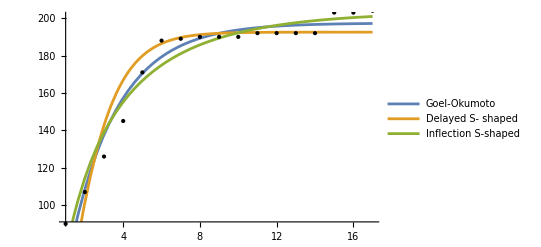

```mathematica
Plot[{goel[t],delayedSshaped[t],inflection[t]},{t,1,17},PlotLegends->{"Goel-Okumoto","Delayed S- shaped","Inflection S-shaped"},PlotStyle->{"red","green","blue"}, Epilog->Point[datamedical]]
```

```mathematica
Grid[{#,goel[#],delayedSshaped[#],inflection[#]}&[{"AIC","BIC","RSquared","AdjustedRSquared"}],Frame->All]
```

AIC | BIC | RSquared | AdjustedRSquared
126.881 | 129.381 | 0.997745 | 0.997444
144.884 | 147.384 | 0.993497 | 0.992629
125.341 | 128.674 | 0.998187 | 0.997799

```mathematica
prediction = Table[{i,Round[inflection[i]]},{i,18,30}]
```

{{18,201},{19,202},{20,202},{21,202},{22,203},{23,203},{24,203},{25,203},{26,203},{27,203},{28,203},{29,203},{30,203}}

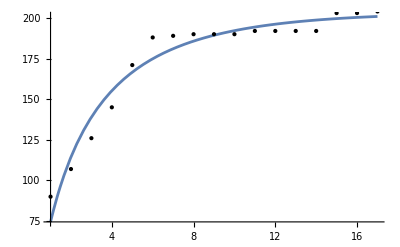

```mathematica
Show[Plot[inflection[t],{t,1,17},Epilog->Point[datamedical]],ListPlot[prediction,PlotStyle->Red]]
```